```mathematica
Clear["Global`*"];
wfly=g(a fz)/((x+y+z)+a fz)-cf fz^2;
wd=(g(x+y+z)/((x+y+z)+a fz)-xi-yi-zi)xi/(xi+ bs yi+cs zi)-(ccd x+cfdd xi)^2;
ws=(g(x+y+z)/((x+y+z)+a fz)-xi-yi-zi)(bs yi)/(xi+ bs yi+cs zi)-(ccd y+cfds yi)^2;
wg=(g(x+y+z)/((x+y+z)+a fz)-xi-yi-zi)(cs zi)/(xi+ bs yi+cs zi)-(ccd z+cfdg zi)^2;
Simplify[{D[wfly,fz]==0,D[wd,x]==0,D[wd,xi]==0,D[ws,y]==0,D[ws,yi]==0,D[wg,z]==0,D[wg,zi]==0}]
```

{(a g (x+y+z))/(a fz+x+y+z)^2==2 cf fz,(a fz g xi)/((a fz+x+y+z)^2 (xi+bs yi+cs zi))==2 ccd (ccd x+cfdd xi),2 cfdd (ccd x+cfdd xi)+(xi (-xi-yi+(g (x+y+z))/(a fz+x+y+z)-zi))/(xi+bs yi+cs zi)^2+xi/(xi+bs yi+cs zi)+(xi+yi-(g (x+y+z))/(a fz+x+y+z)+zi)/(xi+bs yi+cs zi)==0,(a bs fz g yi)/((a fz+x+y+z)^2 (xi+bs yi+cs zi))==2 ccd (ccd y+cfds yi),(bs (-xi-yi+(g (x+y+z))/(a fz+x+y+z)-zi))/(xi+bs yi+cs zi)==2 cfds (ccd y+cfds yi)+(bs^2 yi (-xi-yi+(g (x+y+z))/(a fz+x+y+z)-zi))/(xi+bs yi+cs zi)^2+(bs yi)/(xi+bs yi+cs zi),(a cs fz g zi)/((a fz+x+y+z)^2 (xi+bs yi+cs zi))==2 ccd (ccd z+cfdg zi),(cs (-xi-yi+(g (x+y+z))/(a fz+x+y+z)-zi))/(xi+bs yi+cs zi)==2 cfdg (ccd z+cfdg zi)+(cs^2 (-xi-yi+(g (x+y+z))/(a fz+x+y+z)-zi) zi)/(xi+bs yi+cs zi)^2+(cs zi)/(xi+bs yi+cs zi)}

```mathematica
ClearAll[ff];ff[g_,a_,bs_,n_,ccd_,cfdd_,cfds_,cfdg_,cf_,cs_]:=ff[g,a,bs,n,ccd,cfdd,cfds,cfdg,cf,cs]=FindRoot[{(a g (x+y+z))/(a fz+x+y+z)^2==2 cf fz,(a fz g xi)/((a fz+x+y+z)^2 (xi+bs yi+cs zi))==2 ccd (ccd x+cfdd xi),2 cfdd (ccd x+cfdd xi)+(xi (-xi-yi+(g (x+y+z))/(a fz+x+y+z)-zi))/(xi+bs yi+cs zi)^2+xi/(xi+bs yi+cs zi)+(xi+yi-(g (x+y+z))/(a fz+x+y+z)+zi)/(xi+bs yi+cs zi)==0,(a bs fz g yi)/((a fz+x+y+z)^2 (xi+bs yi+cs zi))==2 ccd (ccd y+cfds yi),(bs (-xi-yi+(g (x+y+z))/(a fz+x+y+z)-zi))/(xi+bs yi+cs zi)==2 cfds (ccd y+cfds yi)+(bs^2 yi (-xi-yi+(g (x+y+z))/(a fz+x+y+z)-zi))/(xi+bs yi+cs zi)^2+(bs yi)/(xi+bs yi+cs zi),(a cs fz g zi)/((a fz+x+y+z)^2 (xi+bs yi+cs zi))==2 ccd (ccd z+cfdg zi),(cs (-xi-yi+(g (x+y+z))/(a fz+x+y+z)-zi))/(xi+bs yi+cs zi)==2 cfdg (ccd z+cfdg zi)+(cs^2 (-xi-yi+(g (x+y+z))/(a fz+x+y+z)-zi) zi)/(xi+bs yi+cs zi)^2+(cs zi)/(xi+bs yi+cs zi)},{x,.5},{xi,0.5},{y,.5},{yi,0.5},{z,0.5},{zi,0.5},{fz,0.6}];
```

Figure 1b

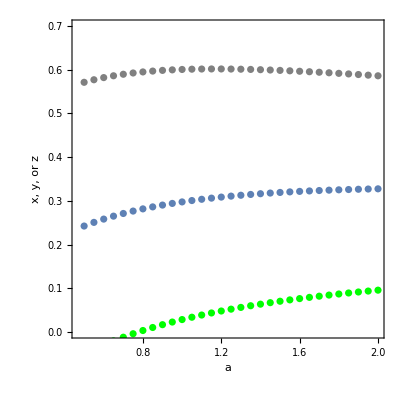

/Users/yuhina1/Dropbox/social thermal/investment1b.pdf

```mathematica
"Figure 1b"
Clear[g,a,bs,n,ccd,cfdd,cfds,cfdg,cf];
g=3;bs= 0.8;n=2;ccd=.5;cfdd=.1;cfds=.3;cfdg=.5;cf=1;cs=0.6;
Table[{a,x/.ff[g,a,bs,n,ccd,cfdd,cfds,cfdg,cf,cs]},{a,0.5,2,0.05}];
g1=ListPlot[%, Axes ->False,Frame->True,FrameLabel->{"a","x, y, or z"},PlotRange->{0,0.7},AspectRatio->1,PlotStyle->Gray];
Table[{a,y/.ff[g,a,bs,n,ccd,cfdd,cfds,cfdg,cf,cs]},{a,0.5,2,0.05}];
g2=ListPlot[%, Axes ->False,Frame->True,FrameLabel->{"a","y"},AspectRatio->1];
Table[{a,z/.ff[g,a,bs,n,ccd,cfdd,cfds,cfdg,cf,cs]},{a,0.5,2,0.05}];
g3=ListPlot[%, Axes ->False,Frame->True,FrameLabel->{"a","z"},PlotRange->{0,0.7},AspectRatio->1,PlotStyle->Green];
Show[g1,g2,g3]
Export["/Users/yuhina1/Dropbox/social thermal/investment1b.pdf",%]
```

Figure 1a

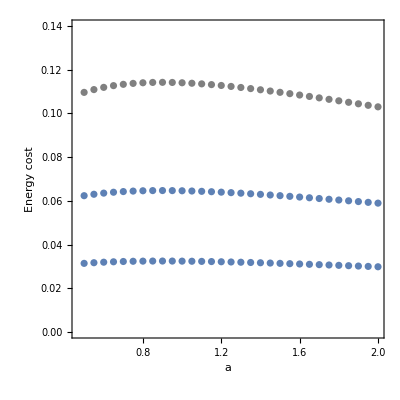

/Users/yuhina1/Dropbox/social thermal/Fig.1aenergetic cost.pdf

```mathematica
"Figure 1a"
Clear[g,a,bs,n,ccd,cfd,cf];
g=3;bs= 0.8;n=2;ccd=.5;cfdd=.1;cfds=.3;cfdg=.5;cf=1;cs=0.6;
Table[{a,(ccd x+cfdd xi)^2/.ff[g,a,bs,n,ccd,cfdd,cfds,cfdg,cf,cs]},{a,0.5,2,0.05}];
g1=ListPlot[%, Axes ->False,Frame->True,FrameLabel->{"a","Energy cost"},PlotRange-> {0,0.14},AspectRatio->1,PlotStyle->Gray];
Table[{a,(ccd y+cfds yi)^2/.ff[g,a,bs,n,ccd,cfdd,cfds,cfdg,cf,cs]},{a,0.5,2,0.05}];
g2=ListPlot[%, Axes ->False,Frame->True,FrameLabel->{"a","Energy cost"},AspectRatio->1];
Table[{a,(ccd z+cfdg zi)^2/.ff[g,a,bs,n,ccd,cfdd,cfds,cfdg,cf,cs]},{a,0.5,2,0.05}];
g3=ListPlot[%, Axes ->False,Frame->True,FrameLabel->{"a","Energy cost"},AspectRatio->1];
Show[g1,g2,g3]
Export["/Users/yuhina1/Dropbox/social thermal/Fig.1aenergetic cost.pdf",%]
```

Figure 1d

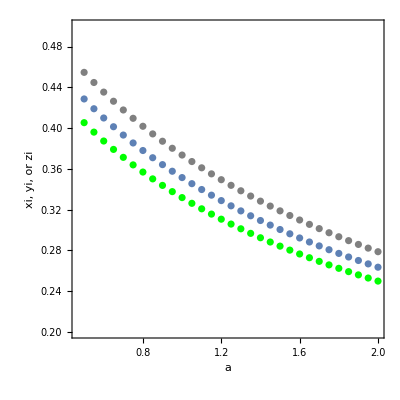

/Users/yuhina1/Dropbox/social thermal/conflict1d.pdf

```mathematica
"Figure 1d"
Clear[g,a,bs,n,ccd,cfd,cf];
g=3;bs= 0.8;n=2;ccd=.5;cfdd=.1;cfds=.3;cfdg=.5;cf=1;cs=0.6;
Table[{a,xi/.ff[g,a,bs,n,ccd,cfdd,cfds,cfdg,cf,cs]},{a,0.5,2,0.05}];
g1=ListPlot[%, Axes ->False,Frame->True,FrameLabel->{"a","xi, yi, or zi"},PlotRange->{0.2,.5},AspectRatio->1,PlotStyle->Gray];
Table[{a,yi/.ff[g,a,bs,n,ccd,cfdd,cfds,cfdg,cf,cs]},{a,0.5,2,0.05}];
g2=ListPlot[%, Axes ->False,Frame->True,FrameLabel->{"a","y"},PlotRange->{0.2,.5},AspectRatio->1];
Table[{a,zi/.ff[g,a,bs,n,ccd,cfdd,cfds,cfdg,cf,cs]},{a,0.5,2,0.05}];
g3=ListPlot[%, Axes ->False,Frame->True,FrameLabel->{"a","z"},PlotRange->{0,.8},AspectRatio->1,PlotStyle->Green];
Show[g1,g2,g3]
Export["/Users/yuhina1/Dropbox/social thermal/conflict1d.pdf",%]
```

Figure 1c

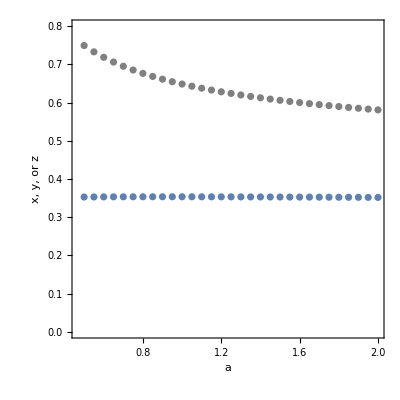

/Users/yuhina1/Dropbox/social thermal/ratio1c.pdf

```mathematica
"Figure 1c"
Clear[g,a,bs,n,ccd,cfd,cf];
g=3;bs= 0.8;n=2;ccd=.5;cfdd=.1;cfds=.3;cfdg=.5;cf=1;cs=0.6;
Table[{a,x/(x+y+z)/.ff[g,a,bs,n,ccd,cfdd,cfds,cfdg,cf,cs]},{a,0.5,2,0.05}];
g1=ListPlot[%, Axes ->False,Frame->True,FrameLabel->{"a","x, y, or z"},PlotRange->{0,.8},AspectRatio->1,PlotStyle->Gray];
Table[{a,xi/(xi+ yi+zi)/.ff[g,a,bs,n,ccd,cfdd,cfds,cfdg,cf,cs]},{a,0.5,2,0.05}];
g2=ListPlot[%, Axes ->False,Frame->True,FrameLabel->{"a","y"},AspectRatio->1];
Show[g1,g2]
Export["/Users/yuhina1/Dropbox/social thermal/ratio1c.pdf",%]
```